## Physics 449 hw#1

Name: Ruojun Wang 
Due: 2018/2/2 W2F

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

## 6) Plot the transmitted probability as a function of k_i

```mathematica
AmpR=(√(1-2(Qki)^2)-1)/(-1-√(1-2(Qki)^2));PTrans=1-AmpR^2; 
Plot[PTrans,{Qki,0,1}]
```

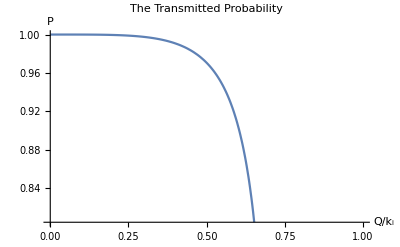

```mathematica
Show[%7,AxesLabel->{HoldForm[Q/Subscript[k, i]],HoldForm[HoldForm[P]]},PlotLabel->HoldForm[The Transmitted Probability]]
```

## 9) Find the energies and eigenstates for motion

```mathematica
Etotal[nx_,ny_]:=nx+1/2+ny^2; (* in the scale of (π^2 ℏ^2)/(2 m^2 a^2) *)

(* Find the 10 lowest energy levels shown in p.259 *)
E1=Etotal[0,1];
E2=Etotal[1,1];
E3=Etotal[2,1];
E4=Etotal[3,1];
E5=Etotal[4,1];
E6=Etotal[5,1];

E7=Etotal[0,2];
E8=Etotal[1,2];
E9=Etotal[2,2];
E10=Etotal[3,2];

Elevels={E1,E2,E3,E4,E5,E6,E7,E8,E9,E10}
```

{3/2,5/2,7/2,9/2,11/2,13/2,9/2,11/2,13/2,15/2}

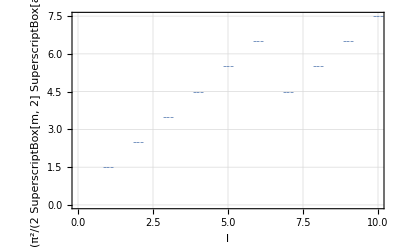

```mathematica
ThadPlot[ListPlot[Elevels,PlotMarkers->"---"],{"l","E(π^2/(2 SuperscriptBox[m, 2] SuperscriptBox[a, 2]))"}]
```

Degeneracies:  n_x=3, n_y=1 and  n_x=0, n_y=2; n_x=4, n_y=1 and n_x=1, n_y=2; n_x=5, n_y=1 and n_x=2, n_y=2